```mathematica
ClearAll["Global`*"]
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]

GenerateA[N1_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,A[[i,j]]=-ⅈ*Subscript[ω, i],
If[i<j,A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, b,i,j]],
A[[i,j]]=-Subscript[g, j,i]*Exp[ⅈ*Subscript[ϕ, b,j,i]]
];
];
]
];
A
]

OperatorVector[Nmodes_]:=Table[Subscript[x, i],{i,1,Nmodes}]~Join~Table[Subscript[p, i],{i,1,Nmodes}];
GenerateB[N1_,m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i==j,If[m!={}&& IntersectingQ[{i},m],A[[i,j]]=Subscript[ω, i]*Exp[-ⅈ*Subscript[ϕ, s,i]],A[[i,j]]=Subscript[ξ, i]*Exp[-ⅈ*Subscript[ϕ, s,i]]]];
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]],A[[i,j]]=Subscript[χ, i,j]*Exp[-ⅈ*Subscript[ϕ, t,i,j]]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=Subscript[g, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]],A[[i,j]]=Subscript[χ, j,i]*Exp[-ⅈ*Subscript[ϕ, t,j,i]]]];
];
];
A
]


SPDC[N1_,m_]:=Module[{A,B,m1,m2,assump},
A=GenerateA[N1];
B=GenerateB[N1,m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=hui∈Reals;
For[i=1,i<=N1,i++,
assump=assump&&Subscript[ω, i]∈Reals&&Subscript[ξ, i]∈Reals&&Subscript[ϕ, s,i]∈Reals;
For[j=i,j<=N1,j++,
If[i!= j,assump=assump&&Subscript[g, i,j]∈Reals&&Subscript[χ, i,j]∈Reals&&Subscript[ϕ, t,i,j]∈Reals&&Subscript[ϕ, b,i,j]∈Reals;]
]];
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

ZeroPhase[Nmodes_]:=Module[{i,j,phases},
phases={};
For[i=1,i<=Nmodes,i++,
phases=phases~Join~{Subscript[ϕ, s,i]->0};
For[j=i,j<=Nmodes,j++,
If[i!= j,phases=phases~Join~{Subscript[ϕ, t,i,j]->0,Subscript[ϕ, b,i,j]->0};]
]];
phases
]

killSPDC[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],(*kill all g_{i,j}*)Flatten@Table[Subscript[g,i,j]->0,{i,1,N1},{j,i+1,N1}],(*kill all chi except pairwise (2j-1,2j)*)Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

killSPDCBS[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

SPDCBS2[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

(* with a phase *)
SPDCBS3[N1_]:=Join[Table[Subscript[ω,i]->0,{i,1,N1}],(*kill all xis*)Table[Subscript[ξ,i]->0,{i,1,N1}],Flatten@Table[If[j==i+1,Subscript[g,i,j]->I g,Subscript[g,i,j]->0],{i,1,N1},{j,i+1,N1}],Flatten@Table[If[j==i+1&&OddQ[i],Subscript[χ,i,j]->-I χ,Subscript[χ,i,j]->0],{i,1,N1},{j,i+1,N1}]];

QFIperPhotonEP[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonEPAnal[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.CovarBasis[Nmodes];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(2 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]

MapThread[Themes`AddThemeRules["LogGrid",#,GridLines->#2,Frame->True]&,{{LogPlot|ListLogPlot,LogLinearPlot|ListLogLinearPlot,LogLogPlot|ListLogLogPlot},{{Automatic,logticks},{logticks,Automatic},logticks}}];
```

```mathematica
Nmodes=2;
EOM=BosonicKitaevChain[Nmodes,0,ϕb=0,χ,ϕχ=0,{}];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
Σin//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
```

(0 | 0 | 0 | χ
0 | 0 | χ | 0
0 | χ | 0 | 0
χ | 0 | 0 | 0)

(cosh(2 t χ) | 0 | sinh(2 t χ) | 0
0 | cosh(2 t χ) | 0 | -sinh(2 t χ)
sinh(2 t χ) | 0 | cosh(2 t χ) | 0
0 | -sinh(2 t χ) | 0 | cosh(2 t χ))

{4 Sinh[2 t χ]^2,2 (p1^2+p2^2+x1^2+x2^2) Cosh[4 t χ]+4 (-p1 p2+x1 x2) Sinh[4 t χ],1/2 (-4+(4+p1^2+p2^2+x1^2+x2^2) Cosh[2 t χ]+(-2 p1 p2+2 x1 x2) Sinh[2 t χ])}

```mathematica
Nmodes=2;
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.{Subscript[g, 1,2]->0,Subscript[ω, 1]->0,Subscript[ω, 2]->0,Subscript[χ, 1,2]->0}//Eigenvalues
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.{Subscript[g, 1,2]->0,Subscript[ω, 1]->0,Subscript[ω, 2]->0,Subscript[χ, 1,2]->0,Subscript[ξ, 2]->0};
EOM//Eigenvalues

DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/2 (Tr[Σout]-2 Nmodes))//FullSimplify


EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.{Subscript[ω, 1]->0,Subscript[ω, 2]->0,Subscript[ξ, 1]->0,Subscript[ξ, 2]->0,Subscript[g, 1,2]->Subscript[χ, 1,2]};
EOM//Eigenvalues

DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/2 (Tr[Σout]-2 Nmodes))//FullSimplify
```

{-ξ_1,ξ_1,-ξ_2,ξ_2}

{-ξ_1,ξ_1,0,0}

4 Cosh[t ξ_1]^2

{0,0,0,0}

4+4 t^2 χ_(1,2)^2

```mathematica
(* Just TMSV N pairs*)
Nmodes=4;
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.killSPDC[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}

1/2 Tr[-Inverse[Σin].G.Σin.G]//Simplify
```

(0 | 0 | 0 | 0 | 0 | χ | 0 | 0
0 | 0 | 0 | 0 | χ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | χ
0 | 0 | 0 | 0 | 0 | 0 | χ | 0
0 | χ | 0 | 0 | 0 | 0 | 0 | 0
χ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | χ | 0 | 0 | 0 | 0
0 | 0 | χ | 0 | 0 | 0 | 0 | 0)

Covariance matrix is

(cosh(2 t χ) | 0 | sinh(2 t χ) | 0 | 0 | 0 | 0 | 0
0 | cosh(2 t χ) | 0 | -sinh(2 t χ) | 0 | 0 | 0 | 0
sinh(2 t χ) | 0 | cosh(2 t χ) | 0 | 0 | 0 | 0 | 0
0 | -sinh(2 t χ) | 0 | cosh(2 t χ) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | cosh(2 t χ) | 0 | sinh(2 t χ) | 0
0 | 0 | 0 | 0 | 0 | cosh(2 t χ) | 0 | -sinh(2 t χ)
0 | 0 | 0 | 0 | sinh(2 t χ) | 0 | cosh(2 t χ) | 0
0 | 0 | 0 | 0 | 0 | -sinh(2 t χ) | 0 | cosh(2 t χ))

{8 Sinh[2 t χ]^2,2 (p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2) Cosh[4 t χ]+4 (-p1 p2-p3 p4+x1 x2+x3 x4) Sinh[4 t χ],-4+1/2 (8+p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2) Cosh[2 t χ]+(-p1 p2-p3 p4+x1 x2+x3 x4) Sinh[2 t χ]}

4 Cosh[4 t χ]

```mathematica
(* Add a BS *)
Nmodes=6;
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.killSPDCBS[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | g | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0
-g | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | g | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0
0 | 0 | -g | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | g | 0 | 0 | 0 | 0 | 0 | χ
0 | 0 | 0 | 0 | -g | 0 | 0 | 0 | 0 | 0 | χ | 0
0 | χ | 0 | 0 | 0 | 0 | 0 | g | 0 | 0 | 0 | 0
χ | 0 | 0 | 0 | 0 | 0 | -g | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | g | 0 | 0
0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | -g | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | g
0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | -g | 0)

Covariance matrix is

((g-χ cosh(2 t √(χ^2-g^2)))/(g-χ) | 0 | (χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (χ cosh(2 t √(χ^2-g^2))+g)/(g+χ) | 0 | -(χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | (χ cosh(2 t √(χ^2-g^2))+g)/(g+χ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | (g-χ cosh(2 t √(χ^2-g^2)))/(g-χ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (g-χ cosh(2 t √(χ^2-g^2)))/(g-χ) | 0 | (χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (χ cosh(2 t √(χ^2-g^2))+g)/(g+χ) | 0 | -(χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | (χ cosh(2 t √(χ^2-g^2))+g)/(g+χ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | (g-χ cosh(2 t √(χ^2-g^2)))/(g-χ) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (g-χ cosh(2 t √(χ^2-g^2)))/(g-χ) | 0 | (χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (χ cosh(2 t √(χ^2-g^2))+g)/(g+χ) | 0 | -(χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2))
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | (χ cosh(2 t √(χ^2-g^2))+g)/(g+χ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(χ sinh(2 t √(χ^2-g^2)))/(√(χ^2-g^2)) | 0 | (g-χ cosh(2 t √(χ^2-g^2)))/(g-χ))

{(24 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2),(12 χ^2 Sinh[t √(-g^2+χ^2)]^2)/(-g^2+χ^2)}

(4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2)

```mathematica
(* for 4 modes *)
F2=(8 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2);
F2n=(4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2);
F4=(16 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2);
F4n=(4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2);
(* For 6 modes *)
F6=(24 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2);
F6n=(4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2);
(* for 8 modes *)
F8=(32 χ^2 (-2 g^2+χ^2+χ^2 Cosh[2 t √(-g^2+χ^2)]) Sinh[t √(-g^2+χ^2)]^2)/((g^2-χ^2)^2);
```

```mathematica
(* Put it at an EP *)
Nmodes=6;
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.killSPDCBS[Nmodes]/.g->χ;
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | χ | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0
-χ | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0
0 | 0 | -χ | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | χ
0 | 0 | 0 | 0 | -χ | 0 | 0 | 0 | 0 | 0 | χ | 0
0 | χ | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0
χ | 0 | 0 | 0 | 0 | 0 | -χ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | χ | 0 | 0
0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | -χ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | χ
0 | 0 | 0 | 0 | χ | 0 | 0 | 0 | 0 | 0 | -χ | 0)

Covariance matrix is

(4 t^2 χ^2+1 | 0 | 2 t χ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | -2 t χ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 t χ | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -2 t χ | 0 | 4 t^2 χ^2+1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 4 t^2 χ^2+1 | 0 | 2 t χ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 t χ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 t χ | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -2 t χ | 0 | 4 t^2 χ^2+1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 t^2 χ^2+1 | 0 | 2 t χ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -2 t χ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 t χ | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 t χ | 0 | 4 t^2 χ^2+1)

{48 (t^2 χ^2+t^4 χ^4),12 t^2 χ^2}

4+4 t^2 χ^2

```mathematica
F2EP=16 (t^2 χ^2+t^4 χ^4);
F2EPn=4+4 t^2 χ^2;
F4EP=32 (t^2 χ^2+t^4 χ^4);
F4EPn=4+4 t^2 χ^2;
F6EP=48 (t^2 χ^2+t^4 χ^4);
F6EPn=4+4 t^2 χ^2;
F8EP=64 (t^2 χ^2+t^4 χ^4);
```

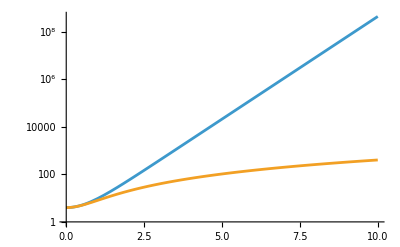

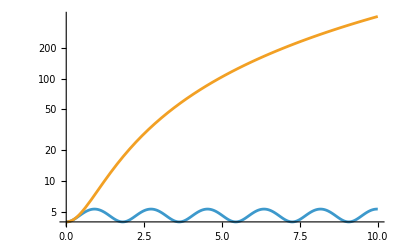

```mathematica
χ=1;g=0.1;
LogPlot[{F2n,F2EPn},{t,0,10}]
χ=1;g=2;
LogPlot[{F2n,F2EPn},{t,0,10}]
```

```mathematica
(* Add correlations *)
Nmodes=3;
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.SPDCBS2[Nmodes];
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//FullSimplify//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | g | 0 | 0 | χ | 0
-g | 0 | g | χ | 0 | 0
0 | -g | 0 | 0 | 0 | 0
0 | χ | 0 | 0 | g | 0
χ | 0 | 0 | -g | 0 | g
0 | 0 | 0 | 0 | -g | 0)

Covariance matrix is

((χ (g+χ) ((χ-g) (g+χ) cosh(2 t √(χ^2-2 g^2))-4 g^2 cosh(t √(χ^2-2 g^2)))+g (4 g^3+5 g^2 χ+g χ^2-χ^3))/((χ^2-2 g^2)^2) | 0 | -(2 χ sinh(t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^(3/2)) | 0 | (4 g χ sinh^2(1/2 t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^2) | 0
0 | (4 g^2 χ (g-χ) cosh(t √(χ^2-2 g^2))+χ (g-χ)^2 (g+χ) cosh(2 t √(χ^2-2 g^2))+g (4 g^3-5 g^2 χ+g χ^2+χ^3))/((χ^2-2 g^2)^2) | 0 | (2 χ sinh(t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^(3/2)) | 0 | -(4 g χ sinh^2(1/2 t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^2)
-(2 χ sinh(t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^(3/2)) | 0 | (χ (g-χ) cosh(2 t √(χ^2-2 g^2))+g (2 g-χ))/(2 g^2-χ^2) | 0 | (4 g χ (g-χ) sinh^2(1/2 t √(χ^2-2 g^2)) sinh(t √(χ^2-2 g^2)))/((χ^2-2 g^2)^(3/2)) | 0
0 | (2 χ sinh(t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^(3/2)) | 0 | (g (2 g+χ)-χ (g+χ) cosh(2 t √(χ^2-2 g^2)))/(2 g^2-χ^2) | 0 | -(4 g χ (g+χ) sinh^2(1/2 t √(χ^2-2 g^2)) sinh(t √(χ^2-2 g^2)))/((χ^2-2 g^2)^(3/2))
(4 g χ sinh^2(1/2 t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^2) | 0 | (4 g χ (g-χ) sinh^2(1/2 t √(χ^2-2 g^2)) sinh(t √(χ^2-2 g^2)))/((χ^2-2 g^2)^(3/2)) | 0 | (4 g^4-3 g^3 χ-g^2 χ (g-χ) (cosh(2 t √(χ^2-2 g^2))-4 cosh(t √(χ^2-2 g^2)))-g^2 χ^2+χ^4)/((χ^2-2 g^2)^2) | 0
0 | -(4 g χ sinh^2(1/2 t √(χ^2-2 g^2)) ((g-χ) (g+χ) cosh(t √(χ^2-2 g^2))+g^2))/((χ^2-2 g^2)^2) | 0 | -(4 g χ (g+χ) sinh^2(1/2 t √(χ^2-2 g^2)) sinh(t √(χ^2-2 g^2)))/((χ^2-2 g^2)^(3/2)) | 0 | (4 g^4+3 g^3 χ+g^2 χ (g+χ) (cosh(2 t √(χ^2-2 g^2))-4 cosh(t √(χ^2-2 g^2)))-g^2 χ^2+χ^4)/((χ^2-2 g^2)^2))

{1/((-2 g^2+χ^2)^4)32 χ^2 (g (-2 g+χ)+χ (-g+χ) Cosh[t √(-2 g^2+χ^2)]) (-g (2 g+χ)+χ (g+χ) Cosh[t √(-2 g^2+χ^2)]) (-3 g^2+χ^2+(-g^2+χ^2) Cosh[t √(-2 g^2+χ^2)]) Sinh[1/2 t √(-2 g^2+χ^2)]^2,(8 χ^2 (-3 g^2+χ^2+(-g^2+χ^2) Cosh[t √(-2 g^2+χ^2)]) Sinh[1/2 t √(-2 g^2+χ^2)]^2)/((-2 g^2+χ^2)^2)}

(4 (g (-2 g+χ)+χ (-g+χ) Cosh[t √(-2 g^2+χ^2)]) (-g (2 g+χ)+χ (g+χ) Cosh[t √(-2 g^2+χ^2)]))/((-2 g^2+χ^2)^2)

```mathematica
EOM/.χ->Sqrt[2] g//Eigensystem
```

{{0,0,0,0,0,0},{{-1/(√2),0,-1/(√2),0,0,1},{1/(√2),0,-1/(√2),1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}}

```mathematica
F2n=(4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2);
F3n=(4 (g (-2 g+χ)+χ (-g+χ) Cosh[t √(-2 g^2+χ^2)]) (-g (2 g+χ)+χ (g+χ) Cosh[t √(-2 g^2+χ^2)]))/((-2 g^2+χ^2)^2);
F3n/F2n//FullSimplify
```

(4 (g-χ) (g+χ) (g (-2 g+χ)+χ (-g+χ) Cosh[t √(-2 g^2+χ^2)]) (-g (2 g+χ)+χ (g+χ) Cosh[t √(-2 g^2+χ^2)]))/((-2 g^2+χ^2)^2 (4 g^2-2 χ^2-2 χ^2 Cosh[2 t √(-g^2+χ^2)]))

```mathematica
(* Add correlations  and EP*)
Nmodes=3;
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.SPDCBS2[Nmodes]/.χ->Sqrt[2] g;
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//FullSimplify//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | g | 0 | 0 | √2 g | 0
-g | 0 | g | √2 g | 0 | 0
0 | -g | 0 | 0 | 0 | 0
0 | √2 g | 0 | 0 | g | 0
√2 g | 0 | 0 | -g | 0 | g
0 | 0 | 0 | 0 | -g | 0)

Covariance matrix is

(1/2 (2+√2) g^2 t^2 (g^2 t^2+4)+1 | 0 | √2 g t (g^2 t^2+2) | 0 | -(g^2 t^2 (g^2 t^2+2))/(√2) | 0
0 | 1-1/2 (√2-2) g^2 t^2 (g^2 t^2+4) | 0 | -√2 g t (g^2 t^2+2) | 0 | (g^2 t^2 (g^2 t^2+2))/(√2)
√2 g t (g^2 t^2+2) | 0 | 1-2 (√2-2) g^2 t^2 | 0 | (√2-2) g^3 t^3 | 0
0 | -√2 g t (g^2 t^2+2) | 0 | 2 (2+√2) g^2 t^2+1 | 0 | -((2+√2) g^3 t^3)
-(g^2 t^2 (g^2 t^2+2))/(√2) | 0 | (√2-2) g^3 t^3 | 0 | 1-1/2 (√2-2) g^4 t^4 | 0
0 | (g^2 t^2 (g^2 t^2+2))/(√2) | 0 | -((2+√2) g^3 t^3) | 0 | 1/2 (2+√2) g^4 t^4+1)

{4 g^2 t^2 (8+18 g^2 t^2+8 g^4 t^4+g^6 t^6),2 g^2 t^2 (4+g^2 t^2)}

4+8 g^2 t^2+2 g^4 t^4

```mathematica
Nmodes=4;
EOM=SPDC[Nmodes,{}]/.ZeroPhase[Nmodes]/.SPDCBS2[Nmodes]/.g->Sqrt[4/5] χ;
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//FullSimplify//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | (2 χ)/(√5) | 0 | 0 | 0 | χ | 0 | 0
-(2 χ)/(√5) | 0 | (2 χ)/(√5) | 0 | χ | 0 | 0 | 0
0 | -(2 χ)/(√5) | 0 | (2 χ)/(√5) | 0 | 0 | 0 | χ
0 | 0 | -(2 χ)/(√5) | 0 | 0 | 0 | χ | 0
0 | χ | 0 | 0 | 0 | (2 χ)/(√5) | 0 | 0
χ | 0 | 0 | 0 | -(2 χ)/(√5) | 0 | (2 χ)/(√5) | 0
0 | 0 | 0 | χ | 0 | -(2 χ)/(√5) | 0 | (2 χ)/(√5)
0 | 0 | χ | 0 | 0 | 0 | -(2 χ)/(√5) | 0)

Covariance matrix is

((9+4 √5) (2 t^2 χ^2-8 t χ sin((2 t χ)/(√5))+9)+4/5 (20+9 √5) (t^2 χ^2-5) cos((2 t χ)/(√5)) | 0 | -2/5 t χ ((5+2 √5) (2 t χ sin((2 t χ)/(√5))-5)+10 (2+√5) cos((2 t χ)/(√5))) | 0 | -2/5 t χ (5 (2+√5) (t χ-2 sin((2 t χ)/(√5)))+2 (5+2 √5) t χ cos((2 t χ)/(√5))) | 0 | -(4 (t^2 χ^2-5) sin((2 t χ)/(√5)))/(√5)-8 t χ cos((2 t χ)/(√5)) | 0
0 | -(4 √5-9) (2 t^2 χ^2+8 t χ sin((2 t χ)/(√5))+9)-4/5 (9 √5-20) (t^2 χ^2-5) cos((2 t χ)/(√5)) | 0 | 2/5 t χ ((2 √5-5) (2 t χ sin((2 t χ)/(√5))+5)-10 (√5-2) cos((2 t χ)/(√5))) | 0 | 2/5 t χ (5 (√5-2) (t χ+2 sin((2 t χ)/(√5)))+2 (2 √5-5) t χ cos((2 t χ)/(√5))) | 0 | (4 (t^2 χ^2-5) sin((2 t χ)/(√5)))/(√5)+8 t χ cos((2 t χ)/(√5))
-2/5 t χ ((5+2 √5) (2 t χ sin((2 t χ)/(√5))-5)+10 (2+√5) cos((2 t χ)/(√5))) | 0 | 2/5 t^2 χ^2 (5-2 √5 cos((2 t χ)/(√5)))+1 | 0 | (4 t^2 χ^2 sin((2 t χ)/(√5)))/(√5) | 0 | 2/5 t χ (5 (√5-2) (t χ+2 sin((2 t χ)/(√5)))+2 (2 √5-5) t χ cos((2 t χ)/(√5))) | 0
0 | 2/5 t χ ((2 √5-5) (2 t χ sin((2 t χ)/(√5))+5)-10 (√5-2) cos((2 t χ)/(√5))) | 0 | 2/5 t^2 χ^2 (2 √5 cos((2 t χ)/(√5))+5)+1 | 0 | -(4 t^2 χ^2 sin((2 t χ)/(√5)))/(√5) | 0 | -2/5 t χ (5 (2+√5) (t χ-2 sin((2 t χ)/(√5)))+2 (5+2 √5) t χ cos((2 t χ)/(√5)))
-2/5 t χ (5 (2+√5) (t χ-2 sin((2 t χ)/(√5)))+2 (5+2 √5) t χ cos((2 t χ)/(√5))) | 0 | (4 t^2 χ^2 sin((2 t χ)/(√5)))/(√5) | 0 | 2/5 t^2 χ^2 (2 √5 cos((2 t χ)/(√5))+5)+1 | 0 | 4 (√5-2) t χ cos((2 t χ)/(√5))-2/5 (2 √5-5) t χ (2 t χ sin((2 t χ)/(√5))+5) | 0
0 | 2/5 t χ (5 (√5-2) (t χ+2 sin((2 t χ)/(√5)))+2 (2 √5-5) t χ cos((2 t χ)/(√5))) | 0 | -(4 t^2 χ^2 sin((2 t χ)/(√5)))/(√5) | 0 | 2/5 t^2 χ^2 (5-2 √5 cos((2 t χ)/(√5)))+1 | 0 | 2/5 t χ ((5+2 √5) (2 t χ sin((2 t χ)/(√5))-5)+10 (2+√5) cos((2 t χ)/(√5)))
-(4 (t^2 χ^2-5) sin((2 t χ)/(√5)))/(√5)-8 t χ cos((2 t χ)/(√5)) | 0 | 2/5 t χ (5 (√5-2) (t χ+2 sin((2 t χ)/(√5)))+2 (2 √5-5) t χ cos((2 t χ)/(√5))) | 0 | 4 (√5-2) t χ cos((2 t χ)/(√5))-2/5 (2 √5-5) t χ (2 t χ sin((2 t χ)/(√5))+5) | 0 | -(4 √5-9) (2 t^2 χ^2+8 t χ sin((2 t χ)/(√5))+9)-4/5 (9 √5-20) (t^2 χ^2-5) cos((2 t χ)/(√5)) | 0
0 | (4 (t^2 χ^2-5) sin((2 t χ)/(√5)))/(√5)+8 t χ cos((2 t χ)/(√5)) | 0 | -2/5 t χ (5 (2+√5) (t χ-2 sin((2 t χ)/(√5)))+2 (5+2 √5) t χ cos((2 t χ)/(√5))) | 0 | 2/5 t χ ((5+2 √5) (2 t χ sin((2 t χ)/(√5))-5)+10 (2+√5) cos((2 t χ)/(√5))) | 0 | (9+4 √5) (2 t^2 χ^2-8 t χ sin((2 t χ)/(√5))+9)+4/5 (20+9 √5) (t^2 χ^2-5) cos((2 t χ)/(√5)))

{32 (5 (4+t^2 χ^2) (61+13 t^2 χ^2)+4 (-5+t^2 χ^2) (81+20 t^2 χ^2) Cos[(2 t χ)/(√5)]+16 (25-30 t^2 χ^2+t^4 χ^4) Cos[(4 t χ)/(√5)]+8 √5 t χ (-((81+20 t^2 χ^2) Sin[(2 t χ)/(√5)])-8 (-5+t^2 χ^2) Sin[(4 t χ)/(√5)])),8 (20+5 t^2 χ^2+4 (-5+t^2 χ^2) Cos[(2 t χ)/(√5)]-8 √5 t χ Sin[(2 t χ)/(√5)])}

(4 (5 (4+t^2 χ^2) (61+13 t^2 χ^2)+4 (-5+t^2 χ^2) (81+20 t^2 χ^2) Cos[(2 t χ)/(√5)]+16 (25-30 t^2 χ^2+t^4 χ^4) Cos[(4 t χ)/(√5)]+8 √5 t χ (-((81+20 t^2 χ^2) Sin[(2 t χ)/(√5)])-8 (-5+t^2 χ^2) Sin[(4 t χ)/(√5)])))/(20+5 t^2 χ^2+4 (-5+t^2 χ^2) Cos[(2 t χ)/(√5)]-8 √5 t χ Sin[(2 t χ)/(√5)])

```mathematica
Nmodes=2;
EOM=SPDC[Nmodes,{}]/.SPDCBS2[Nmodes]/.{Subscript[ϕ, b,1,2]->-π/2,Subscript[ϕ, b,2,3]->-π/2,Subscript[ϕ, t,1,2]->-π/2}/.g-> χ;
EOM//MatrixForm
EOM/.g-> χ//Eigensystem
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//FullSimplify//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | ⅈ χ | 0 | ⅈ χ
ⅈ χ | 0 | ⅈ χ | 0
0 | -ⅈ χ | 0 | -ⅈ χ
-ⅈ χ | 0 | -ⅈ χ | 0)

{{0,0,0,0},{{0,-1,0,1},{-1,0,1,0},{0,0,0,0},{0,0,0,0}}}

Covariance matrix is

(1 | 0 | 0 | 2 t χ
0 | 4 t^2 χ^2+1 | 2 t χ | 0
0 | 2 t χ | 1 | 0
2 t χ | 0 | 0 | 4 t^2 χ^2+1)

{16 (t^2 χ^2+t^4 χ^4),4 t^2 χ^2}

4+4 t^2 χ^2

```mathematica
Nmodes=4;
EOM=SPDC[Nmodes,{}]/.SPDCBS2[Nmodes]/.{Subscript[ϕ, b,1,2]->-π/2,Subscript[ϕ, b,2,3]->-π/2,Subscript[ϕ, t,1,2]->-π/2,Subscript[ϕ, b,3,4]->-π/2,Subscript[ϕ, t,3,4]->-π/2}/.g-> χ;
EOM//MatrixForm
EOM/.g-> χ//Eigensystem
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//FullSimplify//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | ⅈ χ | 0 | 0 | 0 | ⅈ χ | 0 | 0
ⅈ χ | 0 | ⅈ χ | 0 | ⅈ χ | 0 | 0 | 0
0 | ⅈ χ | 0 | ⅈ χ | 0 | 0 | 0 | ⅈ χ
0 | 0 | ⅈ χ | 0 | 0 | 0 | ⅈ χ | 0
0 | -ⅈ χ | 0 | 0 | 0 | -ⅈ χ | 0 | 0
-ⅈ χ | 0 | 0 | 0 | -ⅈ χ | 0 | -ⅈ χ | 0
0 | 0 | 0 | -ⅈ χ | 0 | -ⅈ χ | 0 | -ⅈ χ
0 | 0 | -ⅈ χ | 0 | 0 | 0 | -ⅈ χ | 0)

{{-ⅈ χ,-ⅈ χ,ⅈ χ,ⅈ χ,0,0,0,0},{{1,-1,1,-1,-1,0,0,1},{-2,1,-1,0,2,1,1,0},{-1,-1,-1,-1,1,0,0,1},{-2,-1,-1,0,2,-1,1,0},{0,0,0,-1,0,0,0,1},{-1,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}}

Covariance matrix is

(1 | 0 | 0 | 2 sin(t χ) | 2 (cos(t χ)-1) | 0 | 0 | 4 (sin(t χ)-t χ)
0 | 16 (sin(t χ)-t χ)^2-8 cos(t χ)+9 | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ) | 0 | 0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3) | 4 (sin(t χ)-t χ) | 0
0 | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ) | -8 cos(t χ)+2 cos(2 t χ)+7 | 0 | 0 | 4 sin(t χ) (cos(t χ)-1) | 2 (cos(t χ)-1) | 0
2 sin(t χ) | 0 | 0 | 3-2 cos(2 t χ) | 4 sin(t χ) (cos(t χ)-1) | 0 | 0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3)
2 (cos(t χ)-1) | 0 | 0 | 4 sin(t χ) (cos(t χ)-1) | -8 cos(t χ)+2 cos(2 t χ)+7 | 0 | 0 | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ)
0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3) | 4 sin(t χ) (cos(t χ)-1) | 0 | 0 | 3-2 cos(2 t χ) | 2 sin(t χ) | 0
0 | 4 (sin(t χ)-t χ) | 2 (cos(t χ)-1) | 0 | 0 | 2 sin(t χ) | 1 | 0
4 (sin(t χ)-t χ) | 0 | 0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3) | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ) | 0 | 0 | 16 (sin(t χ)-t χ)^2-8 cos(t χ)+9)

{32 (20+42 t^2 χ^2+8 t^4 χ^4-2 (7+8 t^2 χ^2) Cos[t χ]-(11+24 t^2 χ^2) Cos[2 t χ]+4 Cos[3 t χ]+Cos[4 t χ]+4 t χ (-13-8 t^2 χ^2+8 Cos[t χ]+4 Cos[2 t χ]) Sin[t χ]),-8 (-3-2 t^2 χ^2+2 Cos[t χ]+Cos[2 t χ]+4 t χ Sin[t χ])}

4 (7+4 t^2 χ^2-4 Cos[t χ]-2 Cos[2 t χ]-8 t χ Sin[t χ]+(16 Sin[(t χ)/2]^4)/(-3-2 t^2 χ^2+2 Cos[t χ]+Cos[2 t χ]+4 t χ Sin[t χ]))

```mathematica
Nmodes=4;
EOM=SPDC[Nmodes,{}]/.SPDCBS2[Nmodes]/.{Subscript[ϕ, b,1,2]->-π/2,Subscript[ϕ, b,2,3]->-π/2,Subscript[ϕ, t,1,2]->-π/2,Subscript[ϕ, b,3,4]->-π/2,Subscript[ϕ, t,3,4]->-π/2};
EOM//MatrixForm
EOM//Eigensystem
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
S//TraditionalForm;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
"Covariance matrix is"
Σin//FullSimplify//TraditionalForm
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{F,n}={1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,1/2 (Tr[Σout]-2 Nmodes)//FullSimplify}

F/n//FullSimplify
```

(0 | ⅈ g | 0 | 0 | 0 | ⅈ χ | 0 | 0
ⅈ g | 0 | ⅈ g | 0 | ⅈ χ | 0 | 0 | 0
0 | ⅈ g | 0 | ⅈ g | 0 | 0 | 0 | ⅈ χ
0 | 0 | ⅈ g | 0 | 0 | 0 | ⅈ χ | 0
0 | -ⅈ χ | 0 | 0 | 0 | -ⅈ g | 0 | 0
-ⅈ χ | 0 | 0 | 0 | -ⅈ g | 0 | -ⅈ g | 0
0 | 0 | 0 | -ⅈ χ | 0 | -ⅈ g | 0 | -ⅈ g
0 | 0 | -ⅈ χ | 0 | 0 | 0 | -ⅈ g | 0)

{{1/2 ⅈ (-g-√(5 g^2-4 χ^2)),1/2 ⅈ (-g-√(5 g^2-4 χ^2)),1/2 ⅈ (g-√(5 g^2-4 χ^2)),1/2 ⅈ (g-√(5 g^2-4 χ^2)),1/2 ⅈ (-g+√(5 g^2-4 χ^2)),1/2 ⅈ (-g+√(5 g^2-4 χ^2)),1/2 ⅈ (g+√(5 g^2-4 χ^2)),1/2 ⅈ (g+√(5 g^2-4 χ^2))},{{g/χ,-(g+√(5 g^2-4 χ^2))/(2 χ),-(-g-√(5 g^2-4 χ^2))/(2 χ),-g/χ,-1,0,0,1},{-(2 (g^2+χ^2))/(χ (g+√(5 g^2-4 χ^2))),g/χ,-g/χ,-(g-√(5 g^2-4 χ^2))/(2 χ),(4 g)/(g+√(5 g^2-4 χ^2)),1,1,0},{-g/χ,-(g-√(5 g^2-4 χ^2))/(2 χ),-(g-√(5 g^2-4 χ^2))/(2 χ),-g/χ,1,0,0,1},{(2 (g^2+χ^2))/(χ (-g+√(5 g^2-4 χ^2))),-g/χ,-g/χ,-(-g-√(5 g^2-4 χ^2))/(2 χ),(4 g)/(g-√(5 g^2-4 χ^2)),-1,1,0},{g/χ,-(g-√(5 g^2-4 χ^2))/(2 χ),-(-g+√(5 g^2-4 χ^2))/(2 χ),-g/χ,-1,0,0,1},{(2 (g^2+χ^2))/(χ (-g+√(5 g^2-4 χ^2))),g/χ,-g/χ,-(g+√(5 g^2-4 χ^2))/(2 χ),(4 g)/(g-√(5 g^2-4 χ^2)),1,1,0},{-g/χ,-(g+√(5 g^2-4 χ^2))/(2 χ),-(g+√(5 g^2-4 χ^2))/(2 χ),-g/χ,1,0,0,1},{-(2 (g^2+χ^2))/(χ (g+√(5 g^2-4 χ^2))),-g/χ,-g/χ,-(-g+√(5 g^2-4 χ^2))/(2 χ),(4 g)/(g+√(5 g^2-4 χ^2)),-1,1,0}}}

$Aborted

Covariance matrix is

(1 | 0 | 0 | 2 sin(t χ) | 2 (cos(t χ)-1) | 0 | 0 | 4 (sin(t χ)-t χ)
0 | 16 (sin(t χ)-t χ)^2-8 cos(t χ)+9 | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ) | 0 | 0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3) | 4 (sin(t χ)-t χ) | 0
0 | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ) | -8 cos(t χ)+2 cos(2 t χ)+7 | 0 | 0 | 4 sin(t χ) (cos(t χ)-1) | 2 (cos(t χ)-1) | 0
2 sin(t χ) | 0 | 0 | 3-2 cos(2 t χ) | 4 sin(t χ) (cos(t χ)-1) | 0 | 0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3)
2 (cos(t χ)-1) | 0 | 0 | 4 sin(t χ) (cos(t χ)-1) | -8 cos(t χ)+2 cos(2 t χ)+7 | 0 | 0 | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ)
0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3) | 4 sin(t χ) (cos(t χ)-1) | 0 | 0 | 3-2 cos(2 t χ) | 2 sin(t χ) | 0
0 | 4 (sin(t χ)-t χ) | 2 (cos(t χ)-1) | 0 | 0 | 2 sin(t χ) | 1 | 0
4 (sin(t χ)-t χ) | 0 | 0 | -2 (4 t χ sin(t χ)+cos(t χ)+2 cos(2 t χ)-3) | 8 t χ-6 sin(t χ)+4 sin(2 t χ)-8 t χ cos(t χ) | 0 | 0 | 16 (sin(t χ)-t χ)^2-8 cos(t χ)+9)

{32 (20+42 t^2 χ^2+8 t^4 χ^4-2 (7+8 t^2 χ^2) Cos[t χ]-(11+24 t^2 χ^2) Cos[2 t χ]+4 Cos[3 t χ]+Cos[4 t χ]+4 t χ (-13-8 t^2 χ^2+8 Cos[t χ]+4 Cos[2 t χ]) Sin[t χ]),-8 (-3-2 t^2 χ^2+2 Cos[t χ]+Cos[2 t χ]+4 t χ Sin[t χ])}

4 (7+4 t^2 χ^2-4 Cos[t χ]-2 Cos[2 t χ]-8 t χ Sin[t χ]+(16 Sin[(t χ)/2]^4)/(-3-2 t^2 χ^2+2 Cos[t χ]+Cos[2 t χ]+4 t χ Sin[t χ]))